# Period-Doubling Bifurcation

## Matt Kafker June 6th, 2020

The logistic map is given by the following recursion relation:
	x_(n+1)=r x_n(1-x_n)
In this notebook, we explore the steady-state behavior of this map as we vary r.

Given an initial value x_0, the map may evolve in the following way for different values of r.

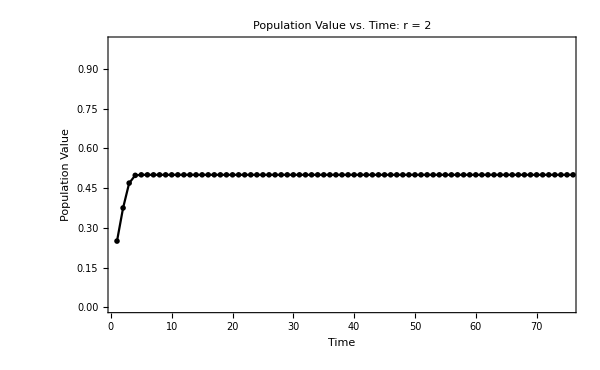
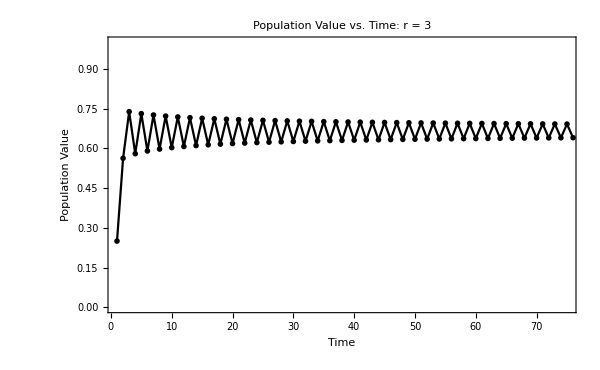
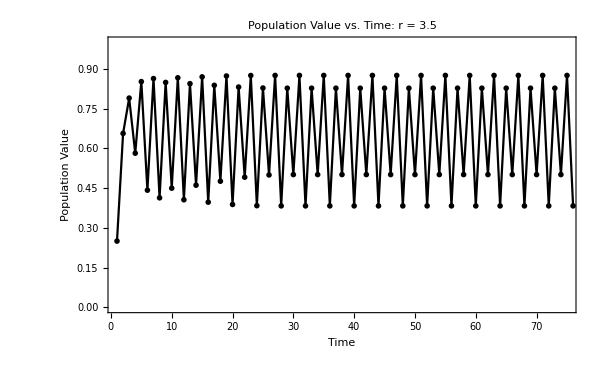
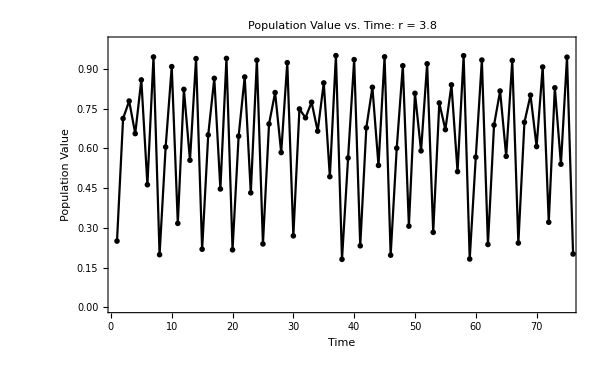

```mathematica
Table[With[{r=r0},ListLinePlot[RecurrenceTable[{x[n+1]==r*x[n](1-x[n]),x[0]==0.25},x,{n,75}],
PlotRange->{{1,75},{0,1}},
PlotLabel->Style[StringJoin["Population Value vs. Time: r = ",ToString@r],18],
Frame->True,
FrameLabel->{Style["Time",15],Style["Population Value",15]},
PlotTheme->"Monochrome",
ImageSize->600]],{r0,{2,3,3.5,3.8}}]
```

Indeed, we see that for smaller values of r, we get relatively simple behavior of our population over time. However, as we increase r, we start to see more complex behavior. And by r = 3.8, there does not appear to be any repetition of our pattern at all.

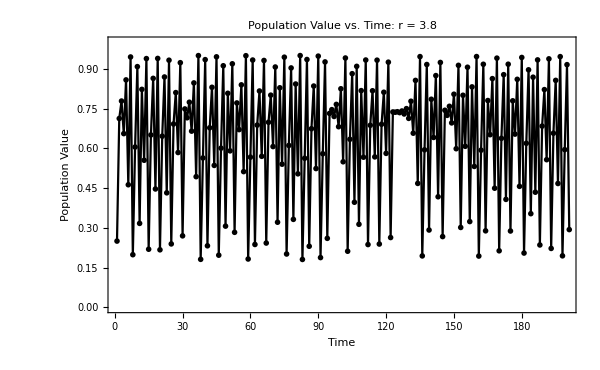

```mathematica
With[{r=3.8},ListLinePlot[RecurrenceTable[{x[n+1]==r*x[n](1-x[n]),x[0]==0.25},x,{n,200}],
PlotRange->{{1,200},{0,1}},
PlotLabel->Style[StringJoin["Population Value vs. Time: r = ",ToString@r],18],
Frame->True,
FrameLabel->{Style["Time",15],Style["Population Value",15]},
PlotTheme->"Monochrome",
ImageSize->600]]
```

Below, we explore precisely how the steady-state population values behave as we vary r.

First, we generate the steady-state population values (expressed as a proportion of 1, the max population value). (Take later times to remove transients.)

```mathematica
genPop[r_,nmax_,start_]:=RecurrenceTable[{x[n+1]==r*x[n](1-x[n]),x[0]==start},x,{n,nmax}][[Floor@nmax/2;;nmax]]
```

We then extract the  values that are repeated.

```mathematica
getEq[pop_]:=DeleteDuplicates@Round[pop,0.001]
```

We pair those values with their corresponding r-value.

```mathematica
getPoints[eq_,r_]:={r,#}&/@eq
```

Finally, we put all those steps together to generate our steady state values at a given value of r.

```mathematica
sim[rInput_]:=Module[{r,allPoints},
r=rInput;
testPop = genPop[r,300,0.05];
testEq = getEq[testPop];
testPoints = getPoints[testEq,r];
Return@testPoints]
```

We plot our results below. To get better resolution, decrease the step size in the table, and the point size in PlotStyle.

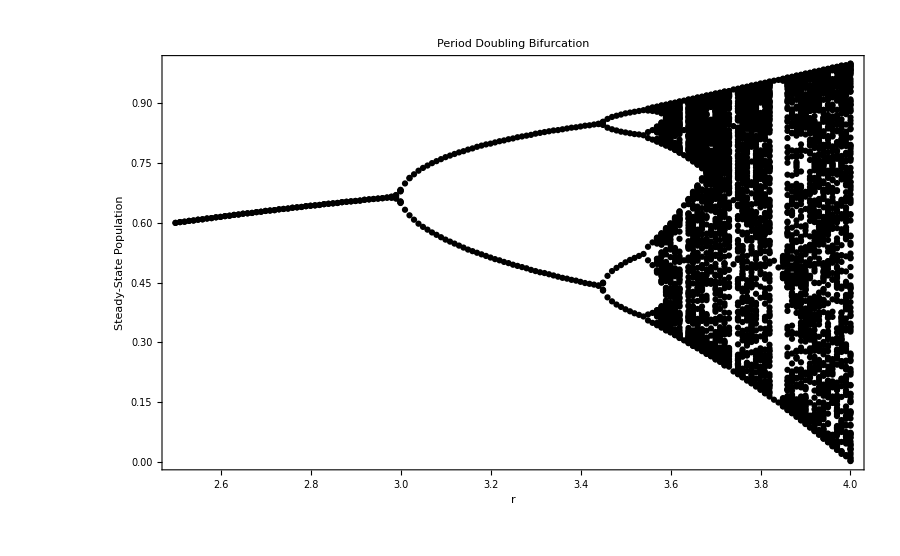

```mathematica
ListPlot[
Table[sim[r],{r,2.5,4,0.01}],
PlotStyle->Directive[Black,PointSize[0.005]],
Frame->True,
PlotLabel->Style["Period Doubling Bifurcation",Black,18],
PlotRange->{{2.5,4},{0,1}},
ImageSize->900,
FrameLabel->{Style["r",Black,15],Style["Steady-State Population",Black,15]}]
```